# QED calculation: Peskin Sec. 5

## e^+e^-→μ^+μ^- (QED): Peskin P.131-136

-Graphics-

### Initialization

You should choose English to avoid unnecessary confusions.

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (21 Feb 2018)

by Thomas Hahn

### Create Topology

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram



FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null)]

```mathematica
topologies=CreateTopologies[0,2->2]
Paint[topologies]
```

### Insert Particles

FeynArts Manual Appendix B has a list of the particles in the (default) SM model.

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes}]
```

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 4 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 4 Classes insertions

TopologyList[Process→{F[2,{1}],-F[2,{1}]}→{F[2,{2}],-F[2,{2}]},Model→{SM},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[2]]],FeynmanGraph[1,Generic==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[2]]]]]

> Top. 1: 4 diagrams

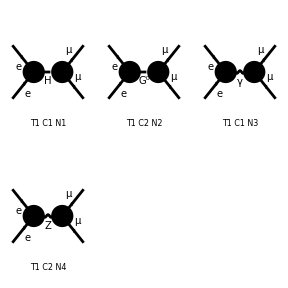

FeynArtsGraphics[{e,e}→{\mu,\mu}][([T1 C1 N1] | [T1 C2 N2] | [T1 C1 N3]
[T1 C2 N4] | Null | Null
Null | Null | Null)]

```mathematica
Paint[diagrams]
```

### Insert Particles (again...)

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

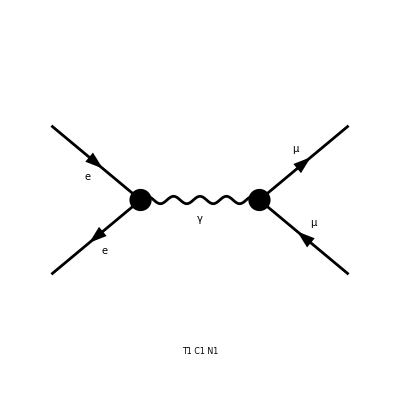

```mathematica
(* We concentrate on QED for simplicity. *)
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA];
matrix=SquaredME[amplitude]//.HelicityME[amplitude]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{FF[F1] FFC[F1] (1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2)+Hel[1] ((Abb4-2 ME2 (Abb1+MM2 Pair5)) Hel[2]+2 Abb8 ME MM Hel[3])+(Abb15-2 MM2 (Abb5+ME2 Pair16)-1/2 (Abb21-2 (Abb7 ME2+(Abb6+2 Abb2 ME2) MM2)) Hel[1] Hel[2]) Hel[3] Hel[4]+2 ME MM (Abb9 Hel[2] Hel[3]+(Abb11 Hel[1]+Abb10 Hel[2]) Hel[4])),{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

```mathematica
(* Assumes unpolarized fermions *)
matrix = matrix//.Hel[_]->0
```

{1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) FF[F1] FFC[F1],{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

-Graphics-

```mathematica
matrix//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}
```

{1/2 (T^2+2 (MM2^2+MM2 (S-T-U))+U^2) FF[F1] FFC[F1],{FF[F1]→-e^2/S,FFC[F1]→-e^2/S}}

```mathematica
%//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta),U->-S-T+2MM2}
```

{1/2 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)) FF[F1] FFC[F1],{FF[F1]→-e^2/(4 EE^2),FFC[F1]→-e^2/(4 EE^2)}}

```mathematica
%[[1]]//.%[[2]]
```

(e^4 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)))/(32 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta}]
```

e^4 ((CosTheta^2 (EE^2-MM2))/(4 EE^2)+(EE^2+MM2)/(4 EE^2))

This is different from Peskin’s book.
Many Traps!!!!!!!!!!!!!!!!

### Doing again with patience.

```mathematica
(*"Weyl" is the default option for CalcFeynAmp, but what is this setting? Let's compare with others.*)
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->Weyl]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-8 Alfa π Sub1 Den[S,0]]

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->Chiral]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[F1]-4 Alfa π Den[S,0] Mat[F2]-4 Alfa π Den[S,0] Mat[F3]-4 Alfa π Den[S,0] Mat[F4]]

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[F1]]

```mathematica
squared = SquaredME[amplitude]
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

Note that, in FormCalc v9.6 (and later), SquaredME returns a list of {squared, squaredRules}, where we should later apply “squaredRules” to “squared”.
This means, here, squared[[1]] is the matrix element squared, and square[[2]] is the rules that applies to  squared[[1]]. See manual for details.
I recommend you to apply this rule as soon as possible (to avoid some confusions).
So what we want is...

```mathematica
squared=SquaredME[amplitude]//.HelicityME[amplitude]
SquaredHelicityME = squared[[1]] //. squared[[2]] //. HelicityME[amplitude]
```

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{FF[F1] FFC[F1] (1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2)+Hel[1] ((Abb4-2 ME2 (Abb1+MM2 Pair5)) Hel[2]+2 Abb5 ME MM Hel[3])+(Abb13-2 MM2 (Abb7+ME2 Pair13)-1/2 (Abb21-2 (Abb6 ME2+(Abb8+2 Abb2 ME2) MM2)) Hel[1] Hel[2]) Hel[3] Hel[4]+2 ME MM (Abb10 Hel[2] Hel[3]+(Abb9 Hel[1]+Abb11 Hel[2]) Hel[4])),{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

16 Alfa2 π^2 Den[S,0]^2 (1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2)+Hel[1] ((Abb4-2 ME2 (Abb1+MM2 Pair5)) Hel[2]+2 Abb5 ME MM Hel[3])+(Abb13-2 MM2 (Abb7+ME2 Pair13)-1/2 (Abb21-2 (Abb6 ME2+(Abb8+2 Abb2 ME2) MM2)) Hel[1] Hel[2]) Hel[3] Hel[4]+2 ME MM (Abb10 Hel[2] Hel[3]+(Abb9 Hel[1]+Abb11 Hel[2]) Hel[4]))

What is “Abb”?

```mathematica
Abbr[]
```

{F1→(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>),Pair10→Pair[s[1],k[2]],Pair3→Pair[s[1],k[3]],Pair1→Pair[s[1],k[4]],Pair5→Pair[s[1],s[2]],Pair8→Pair[s[1],s[3]],Pair6→Pair[s[1],s[4]],Pair11→Pair[s[2],k[1]],Pair2→Pair[s[2],k[3]],Pair4→Pair[s[2],k[4]],Pair7→Pair[s[2],s[3]],Pair9→Pair[s[2],s[4]],Pair17→Pair[s[3],k[1]],Pair15→Pair[s[3],k[2]],Pair12→Pair[s[3],k[4]],Pair13→Pair[s[3],s[4]],Pair16→Pair[s[4],k[1]],Pair18→Pair[s[4],k[2]],Pair14→Pair[s[4],k[3]],Abb7→Pair15 Pair16+Pair17 Pair18,Abb1→Pair1 Pair2+Pair3 Pair4,Abb14→-Pair11 (Pair1 Pair14 Pair15+Pair12 Pair18 Pair3)-Pair10 (Pair12 Pair16 Pair2+Pair14 (-2 Pair11 Pair12+Pair17 Pair4)),Abb2→Pair6 Pair7+Pair8 Pair9,Abb9→Pair10 Pair14-Pair6 S,Abb10→Pair11 Pair12-Pair7 S,Abb5→Pair10 Pair12-Pair8 S,Abb11→Pair11 Pair14-Pair9 S,Abb8→2 Pair10 Pair11 Pair13+2 Abb7 Pair5-2 Pair11 Pair15 Pair6-2 Pair10 Pair16 Pair7-2 Pair11 Pair18 Pair8-2 Pair10 Pair17 Pair9+Pair13 Pair5 (2 ME2-S)+Pair6 Pair7 (-2 ME2+S)+Pair8 Pair9 (-2 ME2+S),Abb6→2 Abb1 Pair13+2 Pair12 Pair14 Pair5-2 Pair12 Pair2 Pair6-2 Pair1 Pair14 Pair7-2 Pair14 Pair4 Pair8-2 Pair12 Pair3 Pair9+Pair13 Pair5 (2 MM2-S)+Pair6 Pair7 (-2 MM2+S)+Pair8 Pair9 (-2 MM2+S),Abb16→Pair12 Pair3 (-2 ME2+S)+Pair10 (Pair17 (-2 MM2+S)-Pair12 (ME2+MM2-T)),Abb19→Pair14 Pair4 (-2 ME2+S)+Pair11 (Pair18 (-2 MM2+S)-Pair14 (ME2+MM2-T)),Abb18→Pair12 Pair2 (-2 ME2+S)+Pair11 (Pair15 (-2 MM2+S)-Pair12 (ME2+MM2-U)),Abb17→Pair1 Pair14 (-2 ME2+S)+Pair10 (Pair16 (-2 MM2+S)-Pair14 (ME2+MM2-U)),Abb13→-2 Abb12-Pair13 (ME2^2+MM2^2-T U),Abb4→2 Abb3-Pair5 (ME2^2+MM2^2-T U),Abb20→Pair12 (Pair14 (4 ME2-S)+2 Pair16 (ME2+2 MM2-S-U))+Pair17 (Pair16 (-4 MM2+2 S)+2 Pair14 (-ME2+U)),Abb15→2 Pair3 (Pair2 (2 ME2-S)+Pair11 (MM2-U))+Pair10 (Pair11 (-4 MM2+S)+2 Pair2 (-2 ME2-MM2+S+U)),Abb21→4 Abb14-2 Abb15 Pair13+2 Abb20 Pair5+2 Abb18 Pair6+2 Abb17 Pair7+2 Abb19 Pair8+2 Abb16 Pair9+Pair6 Pair7 (2 ME2-S) (-2 MM2+S)+Pair8 Pair9 (2 ME2-S) (-2 MM2+S)+Pair13 Pair5 (-2 ME2^2+4 ME2 MM2-2 MM2^2+T^2+4 T U+U^2-2 ME2 (T+U)-2 MM2 (T+U)),Abb12→Pair12 (-ME2 Pair14+Pair16 (ME2-T))+Pair17 (Pair14 (ME2-U)+Pair16 (-2 ME2+T+U)),Abb3→Pair10 (MM2 Pair11+Pair2 (-MM2+T))-Pair3 (Pair11 (MM2-U)+Pair2 (-2 MM2+T+U))}

For example... with “//.” = ReplaceRepeated command,

```mathematica
Abb1//.Abbr[]
```

Pair[s[1],k[4]] Pair[s[2],k[3]]+Pair[s[1],k[3]] Pair[s[2],k[4]]

Hmm... anyway we want to remove the helicity....

```mathematica
SquaredHelicityME//.{Hel[1]->0,Hel[2]->0,Hel[3]->0,Hel[4]->0}
```

8 Alfa2 π^2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) Den[S,0]^2

This is actually THE AVERAGE over the helicity! Because we want to average for the incoming states, while to sum over the outgoing, we have to multiply by four.

```mathematica
MatrixElement=2^2*(SquaredHelicityME//.{Hel[_]->0})
```

32 Alfa2 π^2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) Den[S,0]^2

```mathematica
MatrixElement//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta),U->-T-S+2MM2}
```

(e^4 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)))/(8 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta}]
```

e^4 ((CosTheta^2 (EE^2-MM2))/EE^2+(EE^2+MM2)/EE^2)

-Graphics-